```mathematica
$HistoryLength=0;
SetDirectory[NotebookDirectory[]];
Do[SetOptions[x,{PlotRange->Full,ImageSize->Medium,PlotTheme->"Scientific",BaseStyle->FontSize->15}],{x,{ListLinePlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot}}]
Do[SetOptions[x,{PlotRange->Full,ImageSize->Medium,PlotTheme->"Scientific",BaseStyle->FontSize->15,ExclusionsStyle->Automatic}],{x,{Plot,LogPlot,LogLogPlot}}]
```

```mathematica
compl2Interpret[x_]:=ToExpression[StringReplace[#,{"e"->" 10^","i"->" I"}]]&/@#&/@x
complInterpret[x_]:=ToExpression[StringReplace[#,{"e"->" 10^","i"->" I"}]]&/@x
xx=100000;
refSym=(compl2Interpret@Import["srcSymData.csv","CSV"])[[xx;;-xx]];
srcPermBitData = Import["srcPermBitData.csv","CSV"];
distSym = (compl2Interpret@Import["eqSymOutData.csv","CSV"])[[xx;;-xx]];
```

```mathematica
ComplexListPlot[{eqSymOutData[[;;,1]],srcSymData[[;;,1]]},PlotStyle->{PointSize[0.006],PointSize[0.02]}]
```

-Graphics-

```mathematica
ComplexListPlot[{eqSymOutData[[;;,1]]-srcSymData[[;;,1]]},PlotStyle->PointSize[0.002],Joined->True]
```

-Graphics-

```mathematica
Length[srcPermBitData]
```

1036288

```mathematica
Length[srcSymData]
```

259072

```mathematica
Length[srcSymData[[xx;;-xx]]]
```

258874

```mathematica
Export["srcSymDataMod.txt",{Re[#[[1]]],Im[#[[1]]],Re[#[[2]]],Im[#[[2]]]}&/@srcSymData[[xx;;-xx]],"Table"]
```

srcSymDataMod.txt

```mathematica
Export["eqSymOutDataMod.txt",{Re[#[[1]]],Im[#[[1]]],Re[#[[2]]],Im[#[[2]]]}&/@eqSymOutData[[xx;;-xx]],"Table"]
```

eqSymOutDataMod.txt

```mathematica
30  679/0.3
```

67900.

```mathematica
330000/(50. 1200 3000 10^-9 2700)
```

679.012

```mathematica
Export["srcPermBitDataMod.txt",srcPermBitData,"Table"]
```

srcPermBitDataMod.txt

```mathematica
Length[srcPermBitData]
```

1036288

```mathematica
Length[srcSymData]4
```

1036288

```mathematica
tmp=Transpose@{srcSymData[[;;,1]]//Re,srcSymData[[;;,1]]//Im,(StringJoin@@(ToString/@Reverse[#]))&/@Partition[srcPermBitData[[;;,1]],4]}//DeleteDuplicates
```

{{1,-1,1111},{1,1,1011},{-1,-1,1110},{3,-3,0101},{-1,1,1010},{-3,-1,1100},{-3,1,1000},{1,-3,0111},{3,1,1001},{-3,3,0000},{3,-1,1101},{-3,-3,0100},{1,3,0011},{-1,3,0010},{3,3,0001},{-1,-3,0110}}

```mathematica
("{0b"<>#[[3]]<>","<>ToString[#[[1]]]<>"."<>If[#[[2]]>=0,"+","-"]<>ToString[Abs@#[[2]]]<>".i},\n")&/@tmp//StringJoin
```

{0b1111,1.-1.i},
{0b1011,1.+1.i},
{0b1110,-1.-1.i},
{0b0101,3.-3.i},
{0b1010,-1.+1.i},
{0b1100,-3.-1.i},
{0b1000,-3.+1.i},
{0b0111,1.-3.i},
{0b1001,3.+1.i},
{0b0000,-3.+3.i},
{0b1101,3.-1.i},
{0b0100,-3.-3.i},
{0b0011,1.+3.i},
{0b0010,-1.+3.i},
{0b0001,3.+3.i},
{0b0110,-1.-3.i},

```mathematica
479773./Length[srcPermBitData]
```

0.462973

```mathematica
479773./4
```

119943.

```mathematica
384400. 10^3/(3 30 24 3600)
```

49.4342

```mathematica
√(2. Log[2])
```

1.17741

```mathematica
Solve[(1000 +6400)10^3 x Degree == 10000000.,x]
```

{{x→77.4267}}

```mathematica
2. Pi/8
```

0.785398

```mathematica
(670 +6400.)10^3 (2 Pi)/8/1000
```

5552.77

```mathematica
3/0.5
```

6.

```mathematica
250000  2 8 2 21 21
```

3528000000

```mathematica
Length[refSym]
```

159074

```mathematica
NMSE[ref_,dist_]:=10 Log10[Total@1. Norm[dist-ref]^2/(Total@(Norm[dist]^2))]
```

```mathematica
NMSE[refSym,distSym]
```

-12.706

```mathematica
distSym
```

{{0.74963+0.74688 ⅈ,1.7763+1.4494 ⅈ},{-0.90444-1.3039 ⅈ,-0.75449+1.2107 ⅈ},{0.954+0.84685 ⅈ,1.0616-0.85259 ⅈ},159068,{-3.6502+1.0008 ⅈ,3.8894-0.73703 ⅈ},{-0.069417-3.0574 ⅈ,-1.7797+2.6365 ⅈ},{0.57169-0.29854 ⅈ,-0.86483-3.1389 ⅈ}}
 |  |  |  |

```mathematica
M=5;
```

```mathematica
len = Length[distSym];
bounded[x_]:=If[x<=1,1,If[x>=len,len,x]]
u1[k_,m_,n_]:=distSym[[bounded[k+m],1]]distSym[[bounded[k+n],1]]Conjugate[distSym[[bounded[k+m+n],1]]]
u2[k_,m_,n_]:=distSym[[bounded[k+m],1]]distSym[[bounded[k+n],2]]Conjugate[distSym[[bounded[k+m+n],2]]]
```

```mathematica
U=Table[
Flatten[Table[u1[k,m,n],{m,-M,M},{n,-M,M}]]
~Join~
Flatten[Table[u2[k,m,n],{m,-M,M},{n,-M,M}]],
{k,1,len}];
```

$Aborted

```mathematica
(2M+1)^2 2
```

242

```mathematica
modelData=Import["result.txt","Table",HeaderLines->1]
```

{{0,-12.9198,-12.8885,-12.9041,0.00723457,0.00720406,0.00721931},{1,-12.9903,-12.9566,-12.9734,0.00684759,0.00682661,0.0068371},{2,-13.0586,-13.0289,-13.0438,0.00643769,0.0064892,0.00646345},{3,-13.1185,-13.0875,-13.1029,0.0061613,0.00628529,0.00622329},{4,-13.1669,-13.1331,-13.15,0.00594021,0.00599362,0.00596691},{5,-13.209,-13.18,-13.1945,0.00573627,0.00576107,0.00574867},{6,-13.2563,-13.2263,-13.2413,0.00549417,0.00554377,0.00551897},{7,-13.2994,-13.2738,-13.2866,0.00535126,0.00544474,0.005398},{8,-13.3487,-13.3211,-13.3349,0.00516064,0.00524458,0.00520261},{9,-13.3944,-13.3715,-13.3829,0.00499099,0.00505205,0.00502152},{10,-13.444,-13.425,-13.4345,0.0048366,0.00479463,0.00481562},{11,-13.4942,-13.4751,-13.4846,0.00462687,0.00461161,0.00461924},{12,-13.5459,-13.5267,-13.5363,0.00444003,0.00444193,0.00444098},{13,-13.5991,-13.5762,-13.5877,0.00430278,0.00427034,0.00428656},{14,-13.644,-13.6221,-13.6331,0.00410828,0.00407202,0.00409015},{15,-13.6869,-13.6646,-13.6758,0.00396529,0.00396147,0.00396338},{16,-13.73,-13.7071,-13.7185,0.00378984,0.003849,0.00381942},{17,-13.777,-13.7535,-13.7652,0.00373271,0.00373844,0.00373557},{18,-13.8197,-13.7952,-13.8074,0.00358206,0.00360496,0.00359351},{19,-13.8647,-13.8428,-13.8537,0.00346194,0.00343522,0.00344858}}

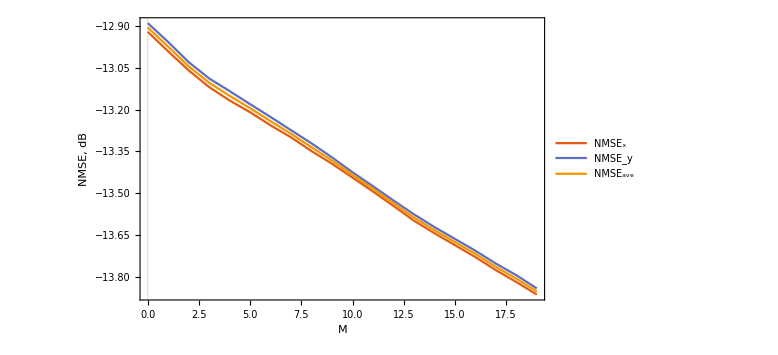

```mathematica
ListLinePlot[Transpose[{{#[[1]],#[[2]]},{#[[1]],#[[3]]},{#[[1]],#[[4]]}}&/@modelData],PlotLegends->Placed[LineLegend[{"NMSE_x","NMSE_y","NMSE_ave"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.8,0.7}],ImageSize->Large,FrameLabel->{"M","NMSE, dB"}]
```